```mathematica
data=Import["/home/stshammi/Desktop/temp/graviton_mass_bound/graviton_bound_input.csv","CSV"] ;(*m1,m2,beta*)
```

```mathematica
H0=(70*10^5*c)/(10^6*3.261636*tyear)/.{c->3*10^8,tyear->3.1536*10^7}
```

20.4163

```mathematica
Dα=z/(H0*Sqrt[ωM+ωΛ])(1-(z/4*(3ωM)/(ωM+ωΛ)+2α))/.{ωM->0.3111,ωΛ->0.6889,z->0.09,α->0} (*Eq.25 of 1603.08955. matter and dark energy denisties are taken from 1807.06209, table2*)
```

0.00431567

```mathematica
ℳ=(data[[All,1]]*tsolar*data[[All,2]]*tsolar)^(3/5)/(data[[All,1]]*tsolar+data[[All,2]]*tsolar)^(1/5)/.tsolar->4.925491*10^-6;
```

```mathematica
λGeo=√(π^2/data[[All,3]]*Dα *ℳ/(1+z))/.z->0.09; (*wavelength in geometric units*)
```

```mathematica
λ=λGeo*3*10^8; (*wavelength in meters*)
```

```mathematica
Mg=h/(λ c)/.{h->6.62607004×10^-34,c->3*10^8}; (*graviton mass in kg*)
```

```mathematica
MgEV=(Mg*c^2)/(1.6022*10^-19)/.{c->3*10^8}; (*graviton mass in electron volt*)
```

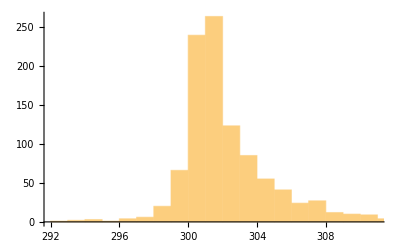

```mathematica
p1=Histogram[MgEV*10^15]
```

```mathematica
Median[MgEV]
```

3.01524×10^-13

```mathematica
Mean[MgEV]
```

3.02226×10^-13

```mathematica
StandardDeviation[MgEV]
```

2.65231×10^-15

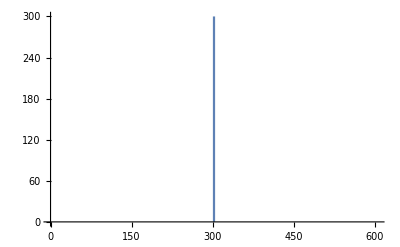

```mathematica
p2=ListLinePlot[{{Mean[MgEV]*10^15,0},{Mean[MgEV]*10^15,300}}]
```

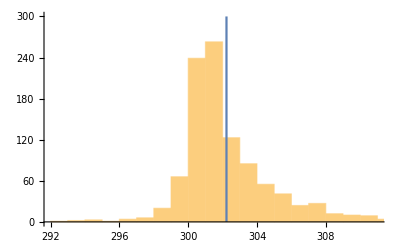

```mathematica
Show[p1,p2]
```

## Graviton mass from the sky-averaged Fisher analysis(based on the old ligo data)

```mathematica
ℳSky=(36.2*tsolar*29.1*tsolar)^(3/5)/((36.2*tsolar)+(29.1*tsolar))^(1/5)/.tsolar->4.925491*10^-6
```

0.000139004

```mathematica
λGeoSky= Sqrt[π^2*Dα*(1/βSky)*1/(1+z)*ℳSky]/.{z->0.09,βSky->3.20221728949451274106611923818985720*10^-2 }
```

0.0130241

```mathematica
λGeoSky= Sqrt[π^2*Dα*(1/βSky)*1/(1+z)*ℳSky]/.{z->0.09,βSky->0.01}
```

0.0233064

```mathematica
λSky=λGeoSky*3*10^8
```

6.99191×10^6

```mathematica
MgSky=h/(λSky c)/.{h->6.62607004×10^-34,c->3*10^8}
```

3.15892×10^-49

```mathematica
MgEVSky=(MgSky*c^2)/(1.6022*10^-19)/.{c->3*10^8}(*graviton mass in electron volt*)
```

1.77445×10^-13